```mathematica
c:=Cos[Pi/5]; s:= Sin[Pi/5];
rho:= c;
areadl= (1+c)(3 c s)/2.0
```

1.29036

```mathematica
rho=Cos[Pi/5];
ee = Sin[Pi/5];
ff = ee/(2rho);
(* side, side, side area *)
area[x_,y_,z_]:= x*y*Sin[arc[x,y,z]]/2;
loc[x_,y_,alpha_]:= Sqrt[x^2+y^2-2x*y*Cos[alpha]];
```

```mathematica
ww[b2_]:= Cos[Pi/5](Sin[Pi/5]-Tan[Pi/5-b2/2]Cos[Pi/5]);
eta;
(* to compute area when eta=r *)
Clear[seta,setb,areta];
seta[a_,b_,r_]:=Module[{x}, (x/.Solve[eta[a,b,x]==r,x])//Max];
setb[a_,b_,r_]:= Module[{x},(x/.Solve[eta[a,b,x]==r,x])//Min];
areta[a_,b_,r_]:= area[a,b,seta[a,b,r]];
```

```mathematica
(* obtuse triangle and neighbor *)
areatrap[r_]:= Module[{u,v},
u=seta[1.75(* was 2rho*),1.75(*was 2rho*),r];
v = seta[2rho,u,r];
area[2rho,2rho,u]+(area[2rho,u,v])];
areatrapObtuse[r_]:= Module[{u,v},
u = seta[2rho,2rho,r];
v = seta[2rho,u,2];
(area[2rho,2rho,u]+area[2rho,u,v])];
```

```mathematica
Clear[ell,ellx,lawsines];

ell[h_,psi_]:= Module[{r,theta},
r = Sqrt[h^2 + rho^2];
theta = ArcCos[h/r];
Sqrt[1+r^2 - 2 *r * Cos[psi+theta]]];

ellx[x_,alpha_]:= ell[ee-x,3Pi/10+alpha];

lawsines[a_,alpha_,beta_,gamma_]:= (a/Sin[alpha]) {Sin[beta],Sin[gamma]};
```

```mathematica
Clear[thetax]; (* debugged, all good, april 30, 2015 *)thetax[xalpha_,alpha_]:= Module[{gamma,h,r,psi,elx,ispos,thetapp,phipp,phi,theta1,theta,thetap},
h = xalpha - ee;
r = Sqrt[h^2+(rho)^2];
psi = ArcSin[h/r];
elx = ellx[xalpha,alpha];
gamma = arc[r,(2ee-xalpha),1];
ispos = (N[(3Pi/10 + alpha + gamma - Pi)]≥ 0.0);
thetapp = arc[elx,1,r];
phipp = arc[elx,r,1];
phi = If[ispos,phipp,-phipp];
theta1 = Pi/5 + phi - psi; 
theta = If[N[theta1]≤ N[Pi/5],theta1,theta1-2Pi/5];
thetap = If[ispos,thetapp,-thetapp];
(* print *)
(* Print[" h ",h," r ",r," psi: ",psi," elx: ",elx," gamma=",gamma," ispos=",ispos," thetapp=",thetapp," phipp=",phipp," phi=",phi," theta1=",theta1]; *)
{theta,thetap}
	];
```

```mathematica
pinwheeledge[alpha_,beta_,xgamma_]:= Module[{gamma,xalpha,xbeta},
gamma = Pi/5 - (alpha+beta);
{xalpha,xbeta}=lawsines[xgamma,2Pi/5-alpha,2Pi/5-beta,2Pi/5-gamma];
{ellx[xalpha,alpha],ellx[xbeta,beta],ellx[xgamma,gamma]}];

pinwheelarea[alpha_,beta_,xgamma_]:= Module[{a,b,c},
{a,b,c}=pinwheeledge[alpha,beta,xgamma];
area[a,b,c]];
```

```mathematica
ljedge[alpha_,beta_,xgamma_]:=
Module[{x1,x2,x3,x4,x5,x6,gamma,alphap,betap,gammap,delta1,delta2},
gamma = 3Pi/5 - (alpha+beta);
alphap = 2Pi/5 - alpha;
betap = 2Pi/5 - beta;
gammap = 2Pi/5 - gamma;
delta1 = Pi - (gammap+2Pi/5);
delta2 = Pi - delta1;
{x1,x2}=lawsines[xgamma,delta1,2Pi/5,gammap];
x3 = 2ee - x1;
{x4,x5}=lawsines[x3,betap,delta2,alphap];
x6 = x5 - x2;
 Print[{"x4",N[x4],"xgamma",N[xgamma]}]; 
{ellx[x4,alpha],ellx[x6,beta],ellx[xgamma,gamma]}
];
ljarea[alpha_,beta_,xgamma_]:=Module[{a,b,c},
{a,b,c}=ljedge[alpha,beta,xgamma];
area[a,b,c]];
(* another version starting with x4 edge *)
ljedgealt[alpha_,beta_,x4_]:=
Module[{x1,x2,x3,xgamma,x5,x6,gamma,alphap,betap,gammap,delta1,delta2},
gamma = 3Pi/5 - (alpha+beta);
alphap = 2Pi/5 - alpha;
betap = 2Pi/5 - beta;
gammap = 2Pi/5 - gamma;
delta1 = Pi - (gammap+2Pi/5);
delta2 = Pi - delta1;
{x3,x5}=lawsines[x4,delta2,betap,alphap];
x1 = 2ee - x3;
{xgamma,x2}=lawsines[x1,2Pi/5,delta1,gammap];
x6 = x5 - x2;
 Print[{"x4",N[x4],"xgamma",N[xgamma]}];
{ellx[x4,alpha],ellx[x6,beta],ellx[xgamma,gamma]}
];
ljareaalt[alpha_,beta_,xalpha_]:=Module[{a,b,c},
{a,b,c}=ljedgealt[alpha,beta,xalpha];
area[a,b,c]];
```

```mathematica
tjedge[alpha_,beta_,xgamma_]:=
Module[{x1,x2,x3,x4,x5,x6,x7,x8,x9,gamma,alphap,betap,gammap,delta1,delta2,delta3,delta4},
gamma = Pi - (alpha+beta);
alphap = 2Pi/5 - alpha;
betap = 2Pi/5 - beta;
gammap = 2Pi/5 - gamma;
delta1 = Pi - (gammap+2Pi/5);
delta2 = Pi - delta1;
delta3 = Pi - (alphap+delta2);
delta4 = Pi - (betap+2Pi/5);
{x1,x2}=lawsines[xgamma,delta1,2Pi/5,gammap];
x3 = 2ee - x1;
{x4,x5}=lawsines[x3,delta3,delta2,alphap];
x6 = 2 ee - (x5 - x2);
{x7,x8}=lawsines[x6,2Pi/5,betap,delta4];
x9 = x4 - x7;
(* Print[{x1,x2,x3,x4,x5,x6,x7,x8,x9}//N]; *)
{ellx[x9,alpha],ellx[x6,beta],ellx[xgamma,gamma]}]; 
tjarea[alpha_,beta_,xgamma_]:=Module[{a,b,c},
{a,b,c}=tjedge[alpha,beta,xgamma];
area[a,b,c]]
```

```mathematica
(* symmetric tj edge is a special symmetric case of tjedge in which xbeta=ee, alpha=gamma, betap ranges from 0 to pi/5. *)
symmetrictjedge[betap_]:= Module[{beta,alpha,alphap,x,y,xalpha,ela},
beta = 2Pi/5 - betap;
alpha = (Pi-beta)/2;
alphap = 2Pi/5 - alpha;
x = 2 ee Sin[betap/2];
y = (2ee - x)/2;
xalpha = y/Cos[alphap];
ela = ellx[xalpha,alpha];
{ela,ela,ellx[2ee,beta]}
];
symmetrictjarea[betap_]:= area @@ symmetrictjedge[betap];
```

```mathematica
Plot[symmetrictjarea[betap],{betap,0,0.02}]
```

```mathematica
symmetrictjedge[0.02]
```

{1.78176,1.78176,1.62971}

```mathematica
NMinimize[{pinwheelarea[alpha,beta,xgamma],0≤ xgamma,xgamma≤ 2ee,0≤ alpha,alpha ≤ beta,beta ≤ Pi/5 - (alpha+beta)},{alpha,beta,xgamma}]

NMinimize[{ljarea[alpha,beta,xgamma],0≤ xgamma,xgamma≤ 2ee,0≤ alpha,alpha≤ 2Pi/5,0 ≤ beta,beta≤ 2Pi/5,Pi/5 ≤ alpha+beta,alpha+beta ≤ 3Pi/5},{alpha,beta,xgamma}]

NMinimize[{tjarea[alpha,beta,xgamma],0≤ xgamma,xgamma≤ 2ee,0≤ alpha,0 ≤ beta,alpha≤ 2Pi/5,beta≤ 2Pi/5,alpha+beta ≤Pi,3Pi/5 ≤ alpha+beta},{alpha,beta,xgamma}]
```

```mathematica
slide[h1_,h2_]:= Module[{ell,m1,m2,alpha1,alpha2,beta,areaSlide},
alpha1 = ArcTan[h1/(2rho)];
alpha2 = ArcTan[h2/(2rho)];
m1 = Sqrt[h1^2 + (2rho)^2];
m2 = Sqrt[h2^2 + (2rho)^2];
beta=2Pi/5 + alpha1+alpha2;
areaSlide = (1/2) m1 m2 Sin[beta];
areaSlide//N];
slideEdge[h1_,h2_]:= Module[{ell,m1,m2,alpha1,alpha2,beta,edgeSlide},
alpha1 = ArcTan[h1/(2rho)];
alpha2 = ArcTan[h2/(2rho)];
m1 = Sqrt[h1^2 + (2rho)^2];
m2 = Sqrt[h2^2 + (2rho)^2];
beta=2Pi/5 + alpha1+alpha2;
edgeSlide = Sqrt[m1^2+m2^2 - 2m1 m2 Cos[beta]];
edgeSlide//N];

slideEta[h1_,h2_]:= Module[{ell,m1,m2,alpha1,alpha2,beta,areaSlide},
alpha1 = ArcTan[h1/(2rho)];
alpha2 = ArcTan[h2/(2rho)];
m1 = Sqrt[h1^2 + (2rho)^2];
m2 = Sqrt[h2^2 + (2rho)^2];
beta=2Pi/5 + alpha1+alpha2;
ell = Sqrt[m1^2+m2^2-2m1 *m2*Cos[beta]];
{slide[h1,h2],eta[m1,m2,ell],ell,m1,m2,beta}];
```

```mathematica
slideOb[h1_,h2_]:= Module[{ell,m1,m2,alpha1,alpha2,beta,areaSlide},
alpha1 = ArcTan[h1/(2rho)];
alpha2 = ArcTan[h2/(2rho)];
m1 = Sqrt[h1^2 + (2rho)^2];
m2 = Sqrt[h2^2 + (2rho)^2];
beta=4Pi/5 - alpha1-alpha2;
areaSlide = (1/2) m1 m2 Sin[beta];
areaSlide//N];

slideObEta[h1_,h2_]:= Module[{ell,m1,m2,alpha1,alpha2,beta,areaSlide},
alpha1 = ArcTan[h1/(2rho)];
alpha2 = ArcTan[h2/(2rho)];
m1 = Sqrt[h1^2 + (2rho)^2];
m2 = Sqrt[h2^2 + (2rho)^2];
beta=4Pi/5 - alpha1-alpha2;
ell = Sqrt[m1^2+m2^2-2m1 *m2*Cos[beta]];
{{slideOb[h1,h2],area[m1,m2,ell]},eta[m1,m2,ell],{ell,m1,m2},beta}];
```

```mathematica
slideEta[0.5,0.5]
```

{1.37607,1.41265,2.71113,1.69353,1.69353,1.85605}

```mathematica
?Circle
```

RowBox[{"Circle", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], ",", StyleBox["r", "TI"]}], "]"}] is a two-dimensional graphics primitive that represents a circle of radius StyleBox["r", "TI"] centered at the point StyleBox["x", "TI"], StyleBox["y", "TI"]. 
RowBox[{"Circle", "[", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], "]"}] gives a circle of radius 1. 
RowBox[{"Circle", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], ",", StyleBox["r", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["θ", "TR"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["θ", "TR"], StyleBox["2", "TR"]]}], "}"}]}], "]"}] gives a circular arc. 
RowBox[{"Circle", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["r", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["r", "TI"], StyleBox["y", "TI"]]}], "}"}]}], "]"}] gives an ellipse with semi-axes of lengths SubscriptBox[StyleBox["r", "TI"], StyleBox["x", "TI"]] and SubscriptBox[StyleBox["r", "TI"], StyleBox["y", "TI"]], oriented parallel to the coordinate axes.

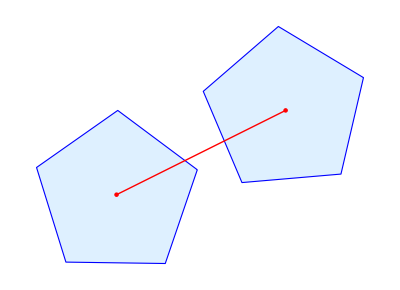

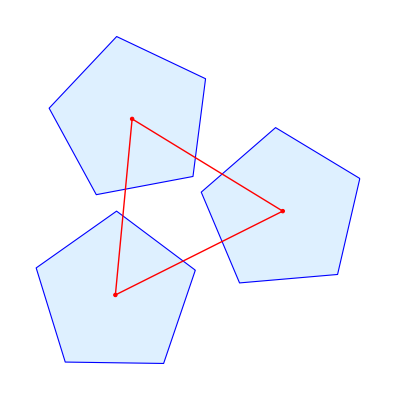

```mathematica
(* Kusner graphics *)
Clear[rtf,rtfw,vert,center];
rtf=RotationMatrix[2Pi/5];
rtfpw[i_]:=MatrixPower[rtf,i].{1,0};
pentvertices=Table[rtfpw[i],{i,0,4}];
movepent[x_,y_,t_]:=({x,y}+#&)/@(RotationMatrix[t].#&/@pentvertices);
pp[x__]:= Polygon@movepent[x];
disk[x__]:= Disk[{x},0.02];
twopent[{x1_,y1_,t1_},{x2_,y2_,t2_}]:= Module[{},
Graphics[{EdgeForm[Blue],LightBlue,pp[x1,y1,t1],pp[x2,y2,t2],Red,EdgeForm[Red],Line[{{x1,y1},{x2,y2}}],disk[x1,y1],disk[x2,y2]}]
];
threepent[{x1_,y1_,t1_},{x2_,y2_,t2_},{x3_,y3_,t3_}]:= Module[{},
Graphics[{EdgeForm[Blue],LightBlue,pp[x1,y1,t1],pp[x2,y2,t2],pp[x3,y3,t3],Red,EdgeForm[Red],Line[{{x1,y1},{x2,y2},{x3,y3},{x1,y1}}],disk[x1,y1],disk[x2,y2],disk[x3,y3]}]
];
delA[dAB_,dAC_,dBC_,thABC_,thBAC_,thCAB_]:= Module[{arcA,A1,A2,B1,B2,C1,C2,thA,thB,thC},
arcA = arc[dAC,dAB,dBC];
{A1,A2} = {0,0};
{B1,B2} = dAB {Cos[arcA],Sin[arcA]};
{C1,C2} = {dAC,0};
thA = arcA+thABC;
thB = arcA + Pi - thBAC;
thC = Pi + thCAB;
threepent[{A1,A2,thA},{B1,B2,thB},{C1,C2,thC}]
];

twopent[{0,0,0.3},{2,1,0.4}]
threepent[{0,0,0.3},{2,1,0.4},{0.2,2.1,0.5}]
(* Graphics[{EdgeForm[Blue],LightBlue,pp[0,0,0.2],pp[2,0,Pi/3],Red,EdgeForm[Red],Line[{{0,0},{2,0}}],disk[0,0],disk[2,0]}] *)
```

```mathematica
area[1.7589,1.667,1.7589]
```

1.29099

```mathematica
a
```

aDL

```mathematica
Solve[area[x,x,2.0*rho]==areadl,x]
```

{{x→-1.78842},{x→1.78842}}

```mathematica
area[1.77949917276633229,1.61803398874989468,1.77949917276633229];
area[1.78832706129201302,1.6181731690803387,1.78832706129201302]
```

1.29036

```mathematica
delA[1.78089,1.6209,1.78089,-0.472466,-0.472466,-0.62586];
delA[1.75890138913909766,1.66701866927780307,1.75890138913909766,-0.496089386802458399,-0.496089386802458399,-0.585367068657158596];
delA[1.76111818043299251,1.64910975362825263,1.76111818043299251,-0.275161314028081583,0.588093394757082888,-0.454012812950737921];
delA[1.77949917276633229,1.61803398874989468,1.77949917276633229,-0.474000063456458676,-0.474000063456458731,0.628318530717958512];
delA[1.76829233385156925,1.65114035269233095,1.76829233385156925,-0.262501121342954558,0.602344871342954558,-0.429315890135415268];
delA[1.76162486509642857,1.62591564086658646,1.76162486509642857,-0.370550473447903372,-0.574995284205013668,-0.532096282908832485];
delA[1.75000000578966652,1.6811990348211312,1.75000000578966652,-0.473934747537161472,-0.525836004456755712,-0.545465318307622238];
```

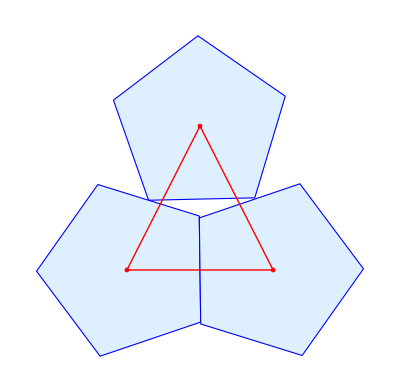

```mathematica
delA[1.74000000574299496,1.69922126844456844,1.74000000574299496,-0.473486957411091147,-0.544805854219826191,-0.517276737005812559];
delA[1.72625441175083205,1.72625440680350861,1.72625441175083205,-0.462126366571889047,0.675866899656889175,-0.456987964052249451];
delA[1.78832706129201302,1.6181731690803387,1.78832706129201302,0.796759498316666259,0.136047412131333922,0.615202738001262572];
delA[1.78824027785957074,1.61830614603291223,1.78824027785957074,0.765369848081597914,0.137838030462401256,0.609978471947414724];
delA[1.78832706129201302,1.61817316908033848,1.78832706129201302,-0.459877563119251,0.136047412131333922,0.61520273800126235];
delA[1.78832706129201302,1.61817316908033848,1.78832706129201302,-0.459877563119251,0.136047412131333922,-0.615202738001262683]
```

```mathematica
area[1.74499,1.705,1.74499]
```

1.29799

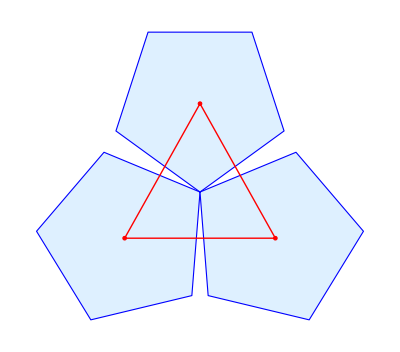

```mathematica
delA[1.74499179474521426,1.70527999813397368,1.74499179474521426,-0.510509030717958612,-0.510509030717958612, -0.549779030717958861]
```

```mathematica
area[1.6835654902267192,1.72,1.83701577962972462]
```

1.31562

1.31571613527541

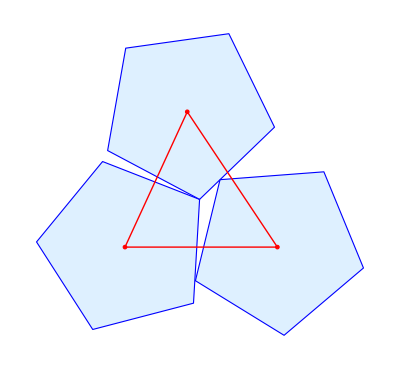

```mathematica
delA[1.69718644975952171,1.81970935764989838,1.69718644975952171,0.650012333231744122,-0.500012400140744107,-0.10845854099872354];
area[1.69718644975952171,1.72000005781575949,1.81970935764989838]
delA[1.69718644975952171,1.72000005781575949,1.81970935764989838,0.650012333231744122,-0.500012400140744107,-0.890189948647242213];
delA[1.6835654902267192,1.72,1.83701577962972462,0.686417986118538104,-0.570219065442197248,-0.866795601142362648]
```

```mathematica
?Polygon
```

RowBox[{"Polygon", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["pt", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["pt", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] is a graphics primitive that represents a filled polygon. 
RowBox[{"Polygon", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["pt", "TI"], StyleBox["11", "TR"]], ",", SubscriptBox[StyleBox["pt", "TI"], StyleBox["12", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["pt", "TI"], StyleBox["21", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] represents a collection of polygons.

```mathematica
?eta
```

eta[x, y, z] circumradius of a triangle with sides x,y,z

```mathematica
NMinimize[{pinwheelarea[alpha,beta,xgamma],0≤ xgamma,xgamma≤ 2ee,0≤ alpha,alpha ≤ beta,beta ≤ Pi/5 - (alpha+beta)},{alpha,beta,xgamma}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{1.23719,{alpha→0.,beta→-1.59059×10^-9,xgamma→0.162413}}

```mathematica
NMinimize[{ljarea[alpha,beta,xgamma],0≤ xgamma,xgamma≤ 2ee,0≤ alpha,alpha≤ 2Pi/5,0 ≤ beta,beta≤ 2Pi/5,Pi/5 ≤ alpha+beta,alpha+beta ≤ 3Pi/5},{alpha,beta,xgamma}];
```

{x5,Cos[0.314159+alpha] (1.17557-0.951057 xgamma Csc[0.628319+alpha+beta]) Sec[0.314159+beta]}

```mathematica
NMinimize[{tjarea[alpha,beta,xgamma],0≤ xgamma,xgamma≤ 2ee,0≤ alpha,0 ≤ beta,alpha≤ 2Pi/5,beta≤ 2Pi/5,alpha+beta ≤Pi,3Pi/5 ≤ alpha+beta},{alpha,beta,xgamma}]
```

{1.23719,{alpha→1.25664,beta→1.25664,xgamma→0.162458}}

```mathematica
f[x_]:= pinwheelarea[Pi/15,Pi/15,x]+ljarea[4Pi/15,0,ee-x];
```

```mathematica
f[0.04]/2
```

1.29287

```mathematica
Plot[pinwheelarea[Pi/15,Pi/15,x],{x,0,ee}]
```

```mathematica
pinwheelarea[Pi/15,Pi/15,0.18]
```

```mathematica
pinwheeledge[Pi/15,Pi/15,0.18]
```

{1.72256,1.72256,1.72256}

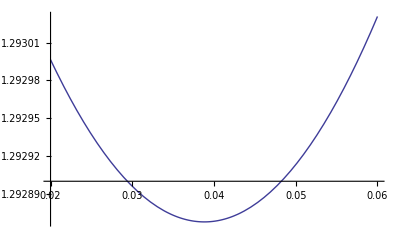

```mathematica
Plot[f[x]/2,{x,0.02,0.06}]
```